# Classifying/Clustering CA

Collect data:

```mathematica
CreateData[range_,init_,t_,preserveBackground_]:=Module[{ca},
ca = If[preserveBackground,CellularAutomaton[#,init,{t,All}]& /@ range, CellularAutomaton[#,init,t]& /@ range];
]
```

## Preprocessing

Cleaning

```mathematica
Conform[data_] := Module[{max, cdata},
	max = Max/@Transpose[Dimensions/@(data)];	
	cdata = CenterArray[#, max]&/@(data);
	cdata
	]
	
Preprocess[data_, n_] := Flatten[data]
```

“Color Negate”

```mathematica
InvertColor[data_]:=Module[{invData,oneArr},
	oneArr = Table[1,{i,Range[Length[data[[1]]]]}];
	invData = Abs[#-oneArr]&/@data
	]
```

Feature Extraction

### Density

```mathematica
DensityFeature[fcellularAuto_]:=Module[{res, aus},
	aus = Counts[fcellularAuto];	
	res = N @ aus[1]/Total[aus]
	
]
```

### Patterns

```mathematica
TRFeature[fcellularAuto_]:= Module[{res}, res=FindTransientRepeat[fcellularAuto,2]]
CountTRFeature[fcellularAuto_, pat_]:= Module[{res}, res = Count[fcellularAuto,pat]]
```

```mathematica
trList1 = TRFeature/@flat1;
trList2 = TRFeature/@flat2;
(*How do I count it?*)
```

### Kurtosis

```mathematica
KurtosisFeature[fcelluraAuot_] := Module[
	{gathered},
	gathered = N[Kurtosis[fcelluraAuot]]
	(*gathered = [gathered==Indeterminate,999]*)
]
```

```mathematica
x = 3;
```

```mathematica
kurtList1 = KurtosisFeature[#]&/@flat1;
kurtList2 = KurtosisFeature[#]&/@flat2;
```

### Extract center column

```mathematica
trcat[data_] := Transpose[data];
ColumnExtract[data_,t_] := #[[t]]&/@trcat[data];
```

```mathematica
columnList1 = ColumnExtract[#]&/@catable;
columnList12= ColumnExtract[#]&/@catable2;
```

### Entropy

```mathematica
EntropyFeature[fcelluraAuot_] := Module[
	{gathered},
	gathered = N@Entropy[fcelluraAuot]
	(*gathered = [gathered==Indeterminate,999]*)
]
```

```mathematica
entropyList1 = EntropyFeature[#]&/@flat1;
entropyList2 = EntropyFeature[#]&/@flat2;
```

### Extract all

```mathematica
ExtractAll[cellularAuto_, t_] := Module[{feat,cc, fcelluraAuot}, 
	fcelluraAuot = Preprocess[cellularAuto, 20];	
	cc = ColumnExtract[cellularAuto,t];
	feat = Flatten[{#[fcelluraAuot]&/@{DensityFeature,KurtosisFeature},EntropyFeature[cc]}]
]
```

Clustering and Classifying

```mathematica
clustering[ca_,n_]:=Module[{ttlabels,fca},
	ttlabels = Thread[Tooltip[Range[Length[ca]], ArrayPlot[#, ImageSize->100]&/@ca]];
	fca = Preprocess[ca,n];
	FindClusters[fca->ttlabels]
]

clusteringArray[ca_,n_]:=Module[{ttlabels,fca},
	ttlabels = ArrayPlot[#, ImageSize->100]&/@ca;
	fca = Preprocess[ca,n];
	FindClusters[fca->ttlabels]
]

classifier[ca_,n_]:=Module[{ttlabels, fca},
	fca = Preprocess[ca,n];
	ClusterClassify[fca]
]

classifierEvaluation[classifier_, ca_, n_] := classifier[preprocess[ca, n]]
```

How to run things

```mathematica
labels =RandomInteger[255,255]
randomInit = RandomInteger[1,50];
t = 50;
catable = CellularAutomaton[#,randomInit,{t,All}]& /@ labels
catable2 =  CellularAutomaton[#,randomInit,t]& /@ labels;
catable2 = Conform[catable2]
```

{178,144,179,109,234,212,214,66,172,165,34,112,182,112,175,83,213,42,162,135,193,101,221,75,255,21,68,126,21,86,88,150,206,182,88,243,47,103,33,143,216,221,76,161,197,62,236,64,242,242,85,1,122,3,216,32,192,43,106,6,255,156,14,253,61,175,172,100,48,198,186,135,0,157,196,123,35,56,45,80,94,198,19,183,165,1,163,187,88,33,20,247,86,7,254,151,48,232,97,171,73,75,69,70,132,75,247,191,180,127,134,44,228,96,215,173,9,18,57,76,210,201,42,123,168,30,29,172,226,144,172,149,53,220,30,101,37,176,152,154,0,68,40,36,115,15,240,18,153,37,53,199,168,128,6,0,75,138,238,57,0,1,193,105,77,52,74,192,213,47,82,120,232,217,45,112,219,165,165,109,12,190,158,100,167,137,229,191,221,208,86,198,193,117,254,194,248,232,62,83,7,70,247,44,212,87,80,52,122,162,168,134,17,103,94,1,90,199,41,6,142,99,0,213,92,173,7,163,191,109,128,238,149,159,51,156,25,53,147,96,24,220,180,8,69,186,39,230,229,125,34,142,47,148,206}

{1}
 |  |  |  |

{1}
 |  |  |  |

```mathematica
dim = 20;
flat1 = Preprocess[catable,dim];
flat2 = Preprocess[Conform[catable2],dim];
```

```mathematica
FeatureSet = ExtractAll[#, t]& /@catable
```

{{0.48902,1.00193,0.692347},{0.124314,6.18613,0.366925},{0.508235,1.00109,0.692347},{0.575294,1.09281,0.680292},{0.904314,8.55663,0.},{0.392157,1.19516,0.673012},{0.68,1.59559,0.653418},{0.164314,4.28254,0.43967},{0.13451,5.58982,0.366925},{0.499608,1.,0.68593},{0.202353,3.19555,0.500402},{0.300392,1.75835,0.610864},{0.713333,1.89024,0.592953},{0.300392,1.75835,0.610864},{0.77098,2.66349,0.526908},{0.52549,1.01042,0.610864},{0.603137,1.17776,0.673012},{0.300392,1.75835,0.610864},{0.221961,2.79058,0.526908},{0.508235,1.00109,0.673012},{0.462353,1.02281,0.664064},{0.493725,1.00063,0.693147},{0.790588,3.04016,0.500402},{0.5,1.,0.673012},{0.986667,73.0135,0.},{0.456863,1.03,0.680292},{0.202353,3.19555,0.500402},{0.510588,1.00179,0.689944},{0.456863,1.03,0.680292},{0.489804,1.00166,0.689944},{0.302745,1.7373,0.610864},{0.496471,1.0002,0.692347},{0.756078,2.42229,0.500402},{0.713333,1.89024,0.592953},{0.302745,1.7373,0.610864},{0.790588,3.04016,0.500402},{0.498824,1.00002,0.626869},{0.548235,1.03758,0.692347},{0.415686,1.11707,0.692347},{0.604706,1.18346,0.673012},{0.800392,3.25921,0.325083},{0.790588,3.04016,0.500402},{0.300392,1.75835,0.610864},{0.538039,1.02329,0.68593},{0.449412,1.04137,0.68593},{0.578431,1.10091,0.610864},{0.398431,1.17216,0.673012},{0.00823529,119.437,0.},{0.58549,1.12046,0.673012},{0.58549,1.12046,0.673012},{0.496471,1.0002,0.626869},{0.418039,1.11045,0.653418},{0.507451,1.00089,0.689944},{0.437647,1.06319,0.692347},{0.800392,3.25921,0.325083},{0.00823529,119.437,0.},{0.00901961,108.879,0.},{0.499608,1.,0.673012},{0.384314,1.22624,0.664064},{0.241176,2.46417,0.526908},{0.986667,73.0135,0.},{0.481176,1.00568,0.693147},{0.389804,1.20421,0.673012},{0.984314,61.7659,0.},{0.53098,1.01542,0.692347},{0.77098,2.66349,0.526908},{0.13451,5.58982,0.366925},{0.147451,4.95487,0.404963},{0.202353,3.19555,0.500402},{0.481176,1.00568,0.693147},{0.58549,1.12046,0.673012},{0.508235,1.00109,0.673012},{0.00627451,157.381,0.},{0.51451,1.00337,0.692347},{0.202745,3.18661,0.500402},{0.614118,1.21982,0.366925},{0.399608,1.16803,0.692347},{0.300392,1.75835,0.610864},{0.489412,1.00179,0.692347},{0.221961,2.79058,0.526908},{0.568235,1.07591,0.68593},{0.481176,1.00568,0.693147},{0.495686,1.0003,0.653418},{0.757647,2.44609,0.592953},{0.499608,1.,0.68593},{0.418039,1.11045,0.653418},{0.389804,1.20421,0.664064},{0.790588,3.04016,0.500402},{0.302745,1.7373,0.610864},{0.415686,1.11707,0.692347},{0.241176,2.46417,0.526908},{0.888627,7.1042,0.325083},{0.489804,1.00166,0.689944},{0.466275,1.01828,0.68593},{0.967451,28.7565,0.},{0.660784,1.46133,0.664064},{0.202353,3.19555,0.500402},{0.319608,1.59857,0.626869},{0.37451,1.2689,0.55108},{0.672941,1.54357,0.626869},{0.498039,1.00006,0.68593},{0.5,1.,0.673012},{0.439608,1.05922,0.68593},{0.481176,1.00568,0.692347},{0.123922,6.21107,0.366925},{0.5,1.,0.673012},{0.888627,7.1042,0.325083},{0.888627,7.1042,0.325083},{0.32902,1.52969,0.626869},{0.516078,1.00414,0.0980391},{0.269804,2.07589,0.526908},{0.147451,4.95487,0.404963},{0.13451,5.58982,0.366925},{0.0133333,73.0135,0.},{0.811373,3.53393,0.526908},{0.71098,1.86648,0.592953},{0.412549,1.12622,0.626869},{0.265098,2.13292,0.55108},{0.499216,1.00001,0.693147},{0.300392,1.75835,0.610864},{0.399216,1.1694,0.653418},{0.671373,1.53245,0.641035},{0.300392,1.75835,0.610864},{0.614118,1.21982,0.366925},{0.0141176,68.8477,0.},{0.496863,1.00016,0.673012},{0.496471,1.0002,0.626869},{0.13451,5.58982,0.366925},{0.32,1.59559,0.626869},{0.124314,6.18613,0.366925},{0.13451,5.58982,0.366925},{0.502353,1.00009,0.592953},{0.466667,1.01786,0.626869},{0.756078,2.42229,0.500402},{0.496863,1.00016,0.673012},{0.493725,1.00063,0.693147},{0.387451,1.21349,0.680292},{0.221961,2.79058,0.526908},{0.164706,4.26861,0.43967},{0.385098,1.22302,0.653418},{0.00627451,157.381,0.},{0.202353,3.19555,0.500402},{0.0133333,73.0135,0.},{0.0482353,18.7824,0.167944},{0.592941,1.14316,0.526908},{0.496471,1.0002,0.626869},{0.32,1.59559,0.626869},{0.265098,2.13292,0.55108},{0.494902,1.00042,0.68593},{0.387451,1.21349,0.680292},{0.466667,1.01786,0.626869},{0.51451,1.00337,0.692347},{0.0141176,68.8477,0.},{0.00666667,148.007,0.},{0.241176,2.46417,0.526908},{0.00627451,157.381,0.},{0.5,1.,0.673012},{0.241569,2.45812,0.55108},{0.942745,15.5265,0.},{0.499216,1.00001,0.693147},{0.00627451,157.381,0.},{0.418039,1.11045,0.653418},{0.462353,1.02281,0.664064},{0.503529,1.0002,0.692347},{0.518824,1.00568,0.692347},{0.242353,2.44609,0.573057},{0.302745,1.7373,0.610864},{0.00901961,108.879,0.},{0.603137,1.17776,0.673012},{0.498824,1.00002,0.626869},{0.370196,1.28907,0.653418},{0.444706,1.04952,0.673012},{0.319608,1.59857,0.626869},{0.84549,4.65483,0.404963},{0.489412,1.00179,0.692347},{0.300392,1.75835,0.610864},{0.944706,16.1436,0.167944},{0.499608,1.,0.68593},{0.499608,1.,0.68593},{0.575294,1.09281,0.680292},{0.202353,3.19555,0.500402},{0.776078,2.75438,0.500402},{0.707451,1.83176,0.610864},{0.147451,4.95487,0.404963},{0.620392,1.24618,0.626869},{0.456471,1.03055,0.689944},{0.784706,2.91917,0.500402},{0.888627,7.1042,0.325083},{0.790588,3.04016,0.500402},{0.241569,2.45812,0.55108},{0.489804,1.00166,0.689944},{0.481176,1.00568,0.693147},{0.462353,1.02281,0.664064},{0.498824,1.00002,0.641035},{0.967451,28.7565,0.},{0.164706,4.26861,0.43967},{0.904314,8.55663,0.},{0.319608,1.59857,0.626869},{0.578431,1.10091,0.610864},{0.52549,1.01042,0.610864},{0.466275,1.01828,0.68593},{0.481176,1.00568,0.692347},{0.888627,7.1042,0.325083},{0.147451,4.95487,0.404963},{0.392157,1.19516,0.673012},{0.525882,1.01075,0.471393},{0.221961,2.79058,0.526908},{0.242353,2.44609,0.573057},{0.507451,1.00089,0.689944},{0.221961,2.79058,0.526908},{0.0141176,68.8477,0.},{0.269804,2.07589,0.526908},{0.437647,1.06319,0.692347},{0.548235,1.03758,0.692347},{0.568235,1.07591,0.68593},{0.418039,1.11045,0.653418},{0.493333,1.00071,0.68593},{0.51451,1.00337,0.692347},{0.364706,1.31601,0.673012},{0.241176,2.46417,0.526908},{0.394902,1.1849,0.673012},{0.499216,1.00001,0.693147},{0.00627451,157.381,0.},{0.603137,1.17776,0.673012},{0.541176,1.02731,0.68593},{0.71098,1.86648,0.592953},{0.466275,1.01828,0.68593},{0.389804,1.20421,0.664064},{0.888627,7.1042,0.325083},{0.575294,1.09281,0.680292},{0.00666667,148.007,0.},{0.942745,15.5265,0.},{0.502353,1.00009,0.592953},{0.810588,3.51318,0.471393},{0.496471,1.0002,0.626869},{0.481176,1.00568,0.693147},{0.453725,1.03456,0.692347},{0.466667,1.01786,0.626869},{0.53098,1.01542,0.664064},{0.0133333,73.0135,0.},{0.164314,4.28254,0.43967},{0.756078,2.42229,0.500402},{0.32902,1.52969,0.626869},{0.00823529,119.437,0.},{0.439608,1.05922,0.68593},{0.58549,1.12046,0.673012},{0.467059,1.01744,0.641035},{0.756863,2.43415,0.500402},{0.784706,2.91917,0.500402},{0.585098,1.11932,0.626869},{0.202353,3.19555,0.500402},{0.394902,1.1849,0.673012},{0.498824,1.00002,0.626869},{0.26902,2.08523,0.610864},{0.756078,2.42229,0.500402}}

```mathematica
c = ClusterClassify[FeatureSet]
```

ClassifierFunction[…]

ClassifierFunction[…]

```mathematica
c = ClusterClassify[FeatureSet, Method->{"NeighborhoodContraction", "NeighborhoodRadius"->1.67}]
```

ClassifierFunction[…]

```mathematica
c = ClusterClassify[FeatureSet, Method->{"MeanShift", "NeighborhoodRadius"->.4}]
```

ClassifierFunction[…]

```mathematica
{{"NeighborhoodRadius"}, {"NeighborsNumber"}}
```

```mathematica
decisionVector = c[FeatureSet]
```

{1,6,1,4,5,1,14,6,6,1,10,7,14,7,3,4,4,7,10,1,1,1,3,1,15,1,10,1,1,1,7,1,3,14,7,3,1,4,1,4,12,3,7,4,1,4,1,2,4,4,1,1,1,1,12,2,2,1,7,10,15,1,1,15,1,3,6,6,10,1,4,1,9,1,10,13,1,7,1,10,4,1,1,14,1,1,7,3,7,1,10,12,1,1,16,14,10,7,7,14,1,1,1,1,6,1,12,12,7,13,10,6,6,8,3,14,1,10,1,7,1,14,7,13,8,1,1,6,7,6,6,1,1,3,1,1,1,10,6,7,9,10,8,6,11,1,7,10,1,1,1,1,8,9,10,9,1,10,5,1,9,1,1,1,1,10,7,2,4,1,7,1,7,12,1,7,5,1,1,4,10,3,14,6,4,1,3,12,3,10,1,1,1,1,16,6,5,7,4,4,1,1,12,6,1,11,10,10,1,10,8,10,1,4,4,1,1,1,7,10,1,1,9,4,4,14,1,7,12,4,9,5,1,3,1,1,1,1,4,8,6,3,7,2,1,4,1,3,3,4,10,1,1,7,3}

```mathematica
clus = Pick[labels, decisionVector, #]&/@DeleteDuplicates[decisionVector]
```

{{178,179,212,165,135,193,101,75,21,126,21,86,150,47,33,197,236,85,1,122,3,43,156,14,61,198,135,157,35,45,198,19,165,1,33,86,7,73,75,69,70,75,9,57,210,30,29,149,53,30,101,37,15,153,37,53,199,75,57,1,193,105,77,47,120,45,165,165,137,86,198,193,117,7,70,212,122,17,1,90,199,142,99,7,149,51,156,25,53,69,39,142,47},{144,66,172,172,100,132,44,228,172,144,172,152,36,100,194,44,24},{109,83,213,103,143,161,62,242,242,186,94,213,109,167,62,83,103,94,213,92,109,147,186,125},{234,238,219,248,238},{214,182,182,183,151,171,173,201,158,173},{34,162,68,6,48,196,80,20,48,134,18,176,68,18,6,138,52,12,208,80,52,162,134,6,34},{112,112,42,88,88,76,106,56,163,88,232,97,180,76,42,226,154,240,74,82,232,112,232,41,163,180,148},{175,221,206,243,221,175,187,215,220,190,229,221,159,220,230,229,206},{255,255,253},{216,216,247,247,191,217,191,247,191},{64,32,192,192,8},{0,0,128,0,0,0,128},{123,127,123},{254,254},{96,168,40,168,168,96},{115,87}}

```mathematica
a = {1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
a
```

{1,2,3,4,5}

```mathematica
clus
```

{{136},{93,25,229,188,152,122,87,24,90,206,13,112,199,232,120,113,125,247,94}}

```mathematica
clus2
```

1
 |  |  |  |

```mathematica
ArrayPlot[CellularAutomaton[#,randomInit,{t,All}],PlotLabel-> #]&/@#&/@clus
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Xor[1,1]
```

False

```mathematica
Xor[0,1]
```

0⊻1

```mathematica
Xor[False,True]
```

True

```mathematica
c2 = InvertColor[catable[[1]]];
```

```mathematica
ArrayPlot[c2]
```

```mathematica
ArrayPlot[catable[[1]]]
```

```mathematica
catable[[1]] = c2;
```

```mathematica
EdgeDe
```

```mathematica
ImageLines
Periodicity
Combination of both
```

```mathematica
l = ImageLines[Rasterize[ArrayPlot[catable[[1]]]]]
```

{{{0.,183.},{360.,183.}},{{72.4708,366.},{194.516,0.}},{{194.516,366.},{72.4708,0.}},{{0.,0.188401},{349.092,366.}},{{0.,365.812},{349.092,0.}},{{163.864,366.},{41.8188,0.}},{{0.,361.451},{120.528,0.}},{{41.8188,366.},{163.864,0.}},831,{{0.,135.45},{201.394,366.}},{{130.008,366.},{171.464,0.}},{{262.822,366.},{283.99,0.}},{{0.,68.6485},{30.371,366.}},{{0.,151.026},{185.712,366.}},{{318.094,366.},{298.946,0.}},{{0.,294.452},{28.4388,0.}}}
 |  |  |  |

```mathematica
slopes = (#[[2]]/#[[1]]&)/@Flatten[Differences/@l, 1]
```

{0.,-2.99889,2.99889,1.04789,-1.04789,2.99889,-2.99889,-2.99889,-2.99889,2.99889,-2.99889,2.99889,1.03642,-1.03642,2.99889,-1.00275,1.04789,0.91816,-2.99889,-4.00244,1.00275,-0.91816,-0.908071,-4.00244,0.908071,-1.18365,2.99889,-1.18365,1.18365,-1.00275,1.00275,-1.00275,4.00244,-6.32501,4.00244,1.19695,-10.9852,-9.28498,-1.19695,-10.9852,12.5082,2.99889,1.23791,-12.5082,-1.32511,-33.0363,-33.0363,-33.0363,-33.0363,-33.0363,33.0363,-33.0363,33.0363,121.167,121.167,27.9504,-72.6974,121.167,27.9504,-24.2202,24.2202,-27.9504,72.6974,51.9236,121.167,1.21042,1.32511,363.509,6.32501,-2.99889,-2.99889,1.23791,-1.23791,27.9504,-2.99889,-27.9504,2.99889,1.00275,-1.00275,10.9852,-0.878397,2.99889,-1.60055,-1.35588,-0.00550197,0.0110043,19.1147,33.0363,1.35588,-0.878397,-1.37162,-72.6974,27.9504,121.167,-72.6974,-40.3817,0.878397,0.868697,2.99889,1.00275,-1.00275,-1.38759,1.52482,-1.50668,-1.9937,1.50668,1.76932,6.81001,-4.00244,1.38759,-2.99889,-1.76932,-1.60055,-0.878397,2.99889,-4.00244,-0.69998,1.60055,-1.8888,4.00244,0.69998,-0.69998,-1.60055,1.60055,-1.60055,-1.15757,1.00275,-1.8888,0.69998,0.69998,-0.69998,0.69998,-0.69998,0.812368,0.69998,-0.69998,0.69998,-0.69998,-1.00275,-2.33657,-4.00244,1.60055,-1.8888,0.803276,-0.803276,2.99889,1.37162,1.8888,4.00244,-2.99889,2.99889,-2.99889,-2.99889,-1.45401,0.69998,1.9937,0.812368,-0.803276,1.45401,-2.99889,1.15757,1.60055,1.9937,1.00275,-1.00275,-1.60055,-0.69998,-0.803276,-1.25194,2.33657,4.00244,1.35588,1.8888,-1.9937,1.8888,2.99889,1.60055,1.9937,-2.44747,1.25194,-1.25194,1.00275,-1.00275,-5.53273,1.45401,2.40953,-2.26727,-5.53273,1.14477,-2.2339,0.803276,-1.26616,5.53273,-2.2339,-2.33657,0.69998,-0.69998,-1.8888,-1.00275,1.00275,2.13853,-1.00275,2.33657,1.60055,-1.60055,0.803276,2.44747,-0.803276,-1.45401,4.00244,-4.00244,1.38759,-2.37257,2.37257,-2.33657,2.37257,5.53273,4.00244,-4.00244,363.509,-6.55876,-6.55876,5.71211,1.68181,1.68181,4.41325,-4.41325,-0.590879,0.590879,-0.812368,0.590879,-0.590879,1.00275,-3.82305,-0.498143,2.99889,1.8888,0.590879,-0.590879,0.590879,-0.590879,-2.99889,-4.00244,0.498143,0.590879,-0.590879,0.590879,-0.590879,0.590879,-0.590879,6.32501,-1.96662,1.45401,4.00244,-4.00244,-2.44747,4.00244,0.590879,-0.590879,0.605822,-0.605822,-1.38759,1.96662,0.590879,-0.69998,-2.99889,-0.498143,-0.821542,0.498143,-0.498143,0.498143,0.498143,-0.498143,-0.498143,1.18365,-1.18365,0.498143,-0.590879,0.69998,-0.69998,0.590879,-0.590879,-1.9937,7.37358,4.00244,1.9937,1.9937,-6.55876,3.82305,0.498143,-0.498143,0.498143,-0.498143,0.498143,-0.498143,-7.37358,13.4386,-7.69111,-1.8888,-1.60055,-1.68181,0.498143,-0.498143,0.498143,-0.498143,0.498143,-0.498143,-8.82847,-4.00244,4.00244,2.44747,2.99889,0.498143,-0.498143,0.498143,-0.498143,0.812368,2.99889,0.868697,1.15757,-1.45401,2.99889,-1.00275,7.37358,1.68181,7.37358,2.37257,-8.41425,-0.0550747,0.69998,1.60055,8.41425,8.41425,8.82847,-1.86392,-1.15757,1.68181,-1.68181,-0.411798,1.00275,-8.82847,-2.99889,0.411798,-0.803276,0.411798,1.00275,2.99889,1.96662,-2.99889,-9.28498,0.411798,-0.411798,0.411798,-0.411798,1.38759,-0.411798,0.411798,-0.411798,0.411798,-0.411798,0.411798,-0.411798,-2.99889,-4.77783,0.411798,0.411798,-0.411798,8.41425,2.99889,-2.37257,0.411798,-0.411798,0.411798,-0.411798,-1.8888,-0.166573,-1.00275,-0.812368,1.96662,-1.68181,-0.235283,-0.411798,0.411798,-0.411798,0.411798,-0.590879,27.9504,-2.99889,-2.37257,0.590879,0.812368,0.166573,0.411798,-0.411798,-0.411798,-0.336517,-1.25194,-12.5082,-4.00244,-4.77783,4.00244,0.300158,0.411798,-0.411798,0.491294,-0.491294,1.18365,0.166573,9.28498,-2.26727,-1.00275,0.803276,1.00275,-10.3539,-10.3539,5.53273,-4.00244,2.33657,-2.33657,4.00244,1.21042,0.166573,-0.166573,0.166573,-0.166573,0.166573,-0.166573,0.348813,5.53273,-5.53273,5.53273,-5.53273,-5.53273,5.53273,4.00244,0.336517,-0.859089,0.69998,-0.69998,0.166573,-0.166573,0.300158,-0.300158,0.300158,-0.300158,0.166573,0.300158,-0.300158,-0.166573,-0.379976,0.300158,-0.300158,0.166573,-0.166573,0.300158,-0.300158,0.300158,-0.300158,0.300158,-0.300158,0.300158,-0.300158,1.38759,-10.3539,2.33657,-0.110485,0.491294,0.235283,0.300158,-0.300158,0.166573,-0.300158,0.300158,-0.300158,0.300158,-0.300158,0.166573,-0.166573,0.300158,-0.300158,0.300158,-0.300158,-0.166573,-5.53273,0.0716471,0.166573,-0.166573,0.166573,-0.166573,0.590879,-4.00244,2.37257,-2.37257,2.37257,-2.33657,-0.628616,1.9937,-0.166573,0.166573,-0.166573,0.166573,-0.166573,0.235283,0.821542,2.99889,0.166573,-0.166573,1.38759,4.00244,-2.99889,4.00244,-4.00244,-0.498143,-0.235283,-1.00275,27.9504,5.53273,-2.2339,5.53273,-1.9937,1.60055,-1.60055,-0.235283,0.235283,9.28498,2.44747,-2.44747,0.235283,-0.235283,0.69998,1.68181,0.166573,-0.166573,-5.53273,-5.53273,-1.21042,0.258634,0.166573,-0.166573,1.00275,-11.6977,10.9852,-1.45401,-1.68181,0.166573,19.1147,2.33657,1.00275,-1.38759,0.121637,-0.411798,-0.733289,-4.00244,-0.127224,-0.590879,-12.5082,9.79064,0.590879,0.060595,-0.060595,0.060595,-0.060595,-0.166573,0.060595,-0.060595,0.060595,-0.060595,0.060595,-0.060595,0.060595,-0.060595,0.060595,-0.060595,0.590879,-0.491294,1.43701,-0.306165,0.411798,0.060595,-0.060595,0.060595,-0.060595,0.0882587,-0.0882587,0.060595,-0.060595,0.060595,-0.060595,-1.00275,-0.868697,-11.6977,0.138422,0.0882587,-0.0882587,0.69998,-0.69998,0.0882587,-0.0882587,1.18365,-0.590879,-1.94013,0.0882587,-0.0882587,-1.21042,1.8888,0.060595,-0.0882587,0.0882587,-0.0882587,0.0882587,-0.0882587,0.060595,-0.060595,-0.840142,-0.306165,0.491294,0.812368,0.0275165,13.4386,3.82305,-0.457592,-0.0165072,0.0110043,-0.0110043,0.0165072,-0.0165072,0.0220112,-0.0220112,-0.0110043,-0.0220112,0.0716471,-0.0716471,5.53273,1.37162,2.33657,1.15757,0.498143,-2.99889,1.60055,-1.60055,2.99889,1.00275,-7.37358,7.37358,-0.386286,-1.60055,-1.37162,3.91082,-1.00275,-2.04967,0.812368,1.96662,-0.235283,1.00275,-1.00275,-1.23791,-5.20483,0.330403,-0.69998,4.00244,-0.590879,14.5175,7.08082,-1.8888,0.590879,-0.0385324,0.373693,0.235283,1.15757,1.60055,1.00275,-14.5175,-0.235283,-0.803276,-1.15757,-7.08082,-5.53273,5.53273,-5.53273,-5.53273,-5.20483,-2.44747,-0.498143,-0.411798,0.450954,-3.82305,0.69998,-2.37257,-0.54005,5.20483,-0.318242,-0.69998,-17.2907,14.5175,1.35588,-1.00275,5.20483,-4.09819,0.312193,0.411798,1.35588,1.96662,0.803276,-10.3539,0.69998,-0.306165,-0.590879,1.00275,2.37257,0.235283,2.44747,-2.44747,-1.00275,1.00275,-5.53273,-0.464263,0.590879,-0.812368,1.18365,0.306165,-0.177903,-1.19695,0.532965,0.812368,-1.38759,1.38759,1.18365,-1.9937,1.60055,8.82847,8.82847,-1.60055,1.60055,-8.41425,8.41425,-3.82305,-0.398986,-0.840142,-1.18365,-1.60055,-9.28498,-0.379976,-4.00244,-1.38759,-0.69998,-0.491294,4.00244,-1.00275,2.99889,-2.99889,-21.3673,0.450954,10.3539,-8.82847,0.491294,-17.2907,0.667681,2.02137,1.38759,1.21042,-0.628616,-1.21042,1.00275,-1.00275,0.878397,19.1147,-1.96662,0.69998,0.0938062,-0.58348,0.547178,1.9937,1.60055,2.44747,-2.44747,1.00275,-0.812368,1.18365,-1.60055,-1.60055,-1.25194,0.58348,-3.82305,-0.306165,-0.878397,-19.1147,-5.53273,0.411798,-2.04967,2.04967,13.4386,2.99889,1.38759,-2.99889,-0.121637,0.812368,1.60055,-0.484483,0.767691,1.38759,-1.38759,0.411798,0.318242,13.4386,-8.82847,-1.23791,5.36394,33.0363,33.0363,-33.0363,-33.0363,33.0363,-27.9504,-27.9504,-27.9504,121.167,27.9504,-121.167,27.9504,363.509,1.15757,1.18365,1.18365,-4.00244,-4.00244,1.19695,10.3539,-5.53273,9.79064,-9.79064,-5.53273,-27.9504,10.9852,1.15757,-9.79064,1.19695,9.79064,10.3539,1.31005,1.14477,-8.82847,-17.2907,9.79064,1.15757,19.1147,-10.3539}

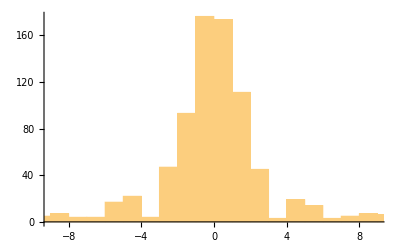

```mathematica
Histogram[slopes]
```

```mathematica
lines = ImageLines[Rasterize[ArrayPlot[#]]]&/@catable;
Length/@(lines);
```

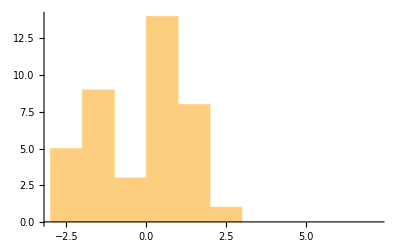

```mathematica
slopes = (#[[2]]/#[[1]]&)/@Flatten[Differences/@(lines[[3]]), 1];
Histogram[slopes]
```

```mathematica
HighlightImage[Rasterize[ArrayPlot[catable[[1]]]],{Red,Line/@l}]
```

-Graphics-

```mathematica
l = ImageLines[Rasterize[ArrayPlot[catable[[4]]]]]
```

```mathematica
Transpose[{HighlightImage[Rasterize[ArrayPlot[catable[[#]]]],{Red,Line/@ImageLines[Rasterize[ArrayPlot[catable[[#]]]]]}]&/@Range[Length[labels]],Rasterize[ArrayPlot[catable[[#]]]]&/@Range[Length[labels]] }]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
lengths = Length/@(lines);
```

```mathematica
lengths
```

{978,68,42,30,22,21,845,59,20,828,49,916,19,52,586,50,41,87,20,59}

```mathematica
c2 = ClusterClassify[lengths, 2]
decisionVector = c2[lengths]
```

ClassifierFunction[…]

{1,2,2,2,2,2,1,2,2,1,2,1,2,2,1,2,2,2,2,2}

```mathematica
$Aborted
```

```mathematica
clus = Pick[labels, decisionVector, #]&/@DeleteDuplicates[decisionVector]
ArrayPlot[CellularAutomaton[#,randomInit,{t,All}],PlotLabel-> #]&/@#&/@clus
```

{{136,122,90,13,232},{93,25,229,188,152,87,24,206,112,199,120,113,125,247,94}}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}